```mathematica
v = v0[y] (x/δ[y]) (1-x/δ[y])^2
```

(x v0[y] (1-x/δ[y])^2)/δ[y]

```mathematica
T0 = T00+γ y
```

T00+y γ

```mathematica
T = T0 + (Tw-T0) (1-x/δ[y])^2
```

T00+y γ+(-T00+Tw-y γ) (1-x/δ[y])^2

```mathematica
momInt =∂_y ∫_0^δ[y] v^2 ⅆx == -ν (D[v, x]/.x->0) + ∫_0^δ[y] g β (T-T0)ⅆx
```

2/105 v0[y] δ[y] v0'[y]+1/105 v0[y]^2 δ'[y]==-(ν v0[y])/δ[y]-1/3 g β (T00-Tw+y γ) δ[y]

```mathematica
egyInt = ∂_y ∫_0^δ[y] v(T-T0)ⅆx==-α (D[T, x]/.x->0)
```

-1/30 γ v0[y] δ[y]-1/30 (T00-Tw+y γ) δ[y] v0'[y]-1/30 (T00-Tw+y γ) v0[y] δ'[y]==(2 α (-T00+Tw-y γ))/δ[y]

```mathematica
nonDimRules = {
y-> yt H,
δ[y]->δt[yt] H RaH^(-1/4),
δ'[y] -> δt'[yt]RaH^(-1/4),
v0[y] -> (α/H)RaH^(1/2) v0t[yt],
v0'[y] -> (α/H^2)RaH^(1/2)v0t'[yt],
γ -> b(Tw-T00)/H,
g-> RaH ν α / (β (Tw-T00)H^3)};
simplifyRules = {
Tw-T00>0,
α>0,H>0,RaH>0,Pr>0};
```

```mathematica
momNonDim = momInt /.nonDimRules //#/.ν->α Pr &// Simplify[#,simplifyRules]&
```

35 Pr (-1+b yt) δt[yt]+v0t[yt] ((105 Pr)/δt[yt]+2 δt[yt] v0t'[yt])+v0t[yt]^2 δt'[yt]==0

```mathematica
momPrInf = momNonDim // #[[1]]/Pr&// Limit[#,Pr->∞]& // #/.b->1&//#==0&
```

(105 v0t[yt])/δt[yt]+35 (-1+yt) δt[yt]==0

```mathematica
v0tSol = Solve[momPrInf,v0t[yt]][[1]][[1]][[2]]
```

-1/3 (-1+yt) δt[yt]^2

```mathematica
egyNonDim = egyInt /.nonDimRules //#/.ν->α Pr & //Simplify[#,simplifyRules]&
```

((-1+b yt) (-60+δt[yt]^2 v0t'[yt]))/δt[yt]+v0t[yt] (b δt[yt]+(-1+b yt) δt'[yt])==0

```mathematica
problemDetails = {b->1,v0t[yt]->v0tSol,v0t'[yt]->D[v0tSol,yt]}
```

{b→1,v0t[yt]→-1/3 (-1+yt) δt[yt]^2,v0t'[yt]→-1/3 δt[yt]^2-2/3 (-1+yt) δt[yt] δt'[yt]}

```mathematica
egyPrInf = egyNonDim //#/.problemDetails& //Simplify[#,{δt[yt]>0}]&
```

(-1+yt) (180+2 δt[yt]^4+3 (-1+yt) δt[yt]^3 δt'[yt])==0

```mathematica
transformationRules = {δt[yt]->Δ[yt]^(1/4), δt'[yt]->Δ'[yt] Δ[yt]^(-3/4)/4}
```

{δt[yt]→Δ[yt]^(1/4),δt'[yt]→Δ'[yt]/(4 Δ[yt]^(3/4))}

```mathematica
ΔP = egyPrInf /. transformationRules //FullSimplify[#,{Δ[yt]>0,yt<1}]&
```

720+8 Δ[yt]+3 (-1+yt) Δ'[yt]==0

```mathematica
Solve[ΔP,Δ'[yt]]
```

{{Δ'[yt]→-(8 (90+Δ[yt]))/(3 (-1+yt))}}

```mathematica
sol = NDSolve[{ΔP,Δ[0]==0},Δ[yt],{yt,0,0.99}]
```

{{Δ[yt]→InterpolatingFunction[…][yt]}}

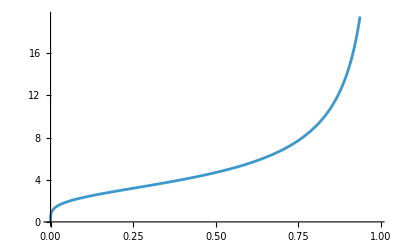

```mathematica
Plot[Evaluate[Δ[yt]^(1/4)/.sol],{yt,0,0.99}]
```

```mathematica
hy = ((-κ D[T,x]/.x->0)/(Tw-T00)) // #/.nonDimRules&//#/.transformationRules&//Simplify[#,Tw>T00]& // #/.problemDetails&
```

-(2 RaH^(1/4) (-1+yt) κ)/(H Δ[yt]^(1/4))

```mathematica
hyNonDim = hy H / (κ RaH^(1/4))
```

-(2 (-1+yt))/Δ[yt]^(1/4)

```mathematica
hMeanNonDim = NIntegrate[hyNonDim /.sol,{yt,0,1}]
```

{0.324668}

```mathematica
NuMean = hMeanNonDim[[1]] RaH^(1/4)
```

0.324668 RaH^(1/4)

```mathematica
NuLiterature = 0.337 RaH^(1/4)
```

0.337 RaH^(1/4)

```mathematica
deviation = (1-NuMean/NuLiterature)
```

0.0365936